## Preamble

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
?gPolygon
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
(* <<TestAlgebra`  *)
<<Geometry`
```

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## DivisorsByBox

## Overview

```mathematica
Map[#&,IntegerPartitions[5]]
Map[#&,Map[#+1&,IntegerPartitions[5]]]
Map[Times@@#&,Map[#+1&,IntegerPartitions[5]]]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

{{6},{5,2},{4,3},{4,2,2},{3,3,2},{3,2,2,2},{2,2,2,2,2}}

{6,10,12,16,18,24,32}

## tmp-1

```mathematica
Map[#&,IntegerPartitions[6]]
GroupBy[Map[#&,IntegerPartitions[6]],Length]
Values[GroupBy[Map[#&,IntegerPartitions[6]],Length]]
Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]
Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

<|1→{{6}},2→{{5,1},{4,2},{3,3}},3→{{4,1,1},{3,2,1},{2,2,2}},4→{{3,1,1,1},{2,2,1,1}},5→{{2,1,1,1,1}},6→{{1,1,1,1,1,1}}|>

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

{{7},{6,2},{5,3},{4,4},{5,2,2},{4,3,2},{3,3,3},{4,2,2,2},{3,3,2,2},{3,2,2,2,2},{2,2,2,2,2,2}}

{7,12,15,16,20,24,27,32,36,48,64}

```mathematica
fDivisorsByBox[n_]:=Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[n]],Length]],1]]
Table[fDivisorsByBox[k],{k,10}]//TableForm
```

2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3 | 4 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 6 | 8 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 8 | 9 | 12 | 16 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 | 10 | 12 | 16 | 18 | 24 | 32 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 12 | 15 | 16 | 20 | 24 | 27 | 32 | 36 | 48 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8 | 14 | 18 | 20 | 24 | 30 | 32 | 36 | 40 | 48 | 54 | 64 | 72 | 96 | 128 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9 | 16 | 21 | 24 | 25 | 28 | 36 | 40 | 45 | 48 | 48 | 60 | 64 | 72 | 81 | 80 | 96 | 108 | 128 | 144 | 192 | 256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 | 18 | 24 | 28 | 30 | 32 | 42 | 48 | 54 | 50 | 60 | 64 | 56 | 72 | 80 | 90 | 96 | 108 | 96 | 120 | 128 | 144 | 162 | 160 | 192 | 216 | 256 | 288 | 384 | 512 |  |  |  |  |  |  |  |  |  |  |  | 
11 | 20 | 27 | 32 | 35 | 36 | 36 | 48 | 56 | 63 | 60 | 72 | 75 | 80 | 64 | 84 | 96 | 108 | 100 | 120 | 135 | 128 | 144 | 112 | 144 | 160 | 180 | 192 | 216 | 243 | 192 | 240 | 256 | 288 | 324 | 320 | 384 | 432 | 512 | 576 | 768 | 1024

{{2},{3,4},{4,6,8},{5,8,9,12,16},{6,10,12,16,18,24,32},{7,12,15,16,20,24,27,32,36,48,64},{8,14,18,20,24,30,32,36,40,48,54,64,72,96,128},{9,16,21,24,25,28,36,40,45,48,48,60,64,72,81,80,96,108,128,144,192,256},{10,18,24,28,30,32,42,48,54,50,60,64,56,72,80,90,96,108,96,120,128,144,162,160,192,216,256,288,384,512},{11,20,27,32,35,36,36,48,56,63,60,72,75,80,64,84,96,108,100,120,135,128,144,112,144,160,180,192,216,243,192,240,256,288,324,320,384,432,512,576,768,1024}}

## tmp-2

```mathematica
sortByNumberOfDivisors[ls_]:=Times@@(ls+1)
fNumberOfDivisorsByPartition[n_]:=Map[Times@@(#+1)&,SortBy[IntegerPartitions[n],sortByNumberOfDivisors[#]&]]
Table[fNumberOfDivisorsByPartition[k],{k,13,13}]
```

{{14,26,36,44,48,50,54,56,66,80,88,90,90,96,98,108,120,120,126,128,140,144,144,150,160,160,162,168,192,210,216,216,216,224,240,250,252,256,270,280,288,288,288,288,300,320,336,360,378,384,384,400,432,448,450,480,480,486,504,512,512,540,576,576,600,640,648,672,720,768,768,800,810,864,864,896,960,972,1024,1080,1152,1152,1280,1296,1440,1458,1536,1536,1728,1920,1944,2048,2304,2560,2592,3072,3456,4096,4608,6144,8192}}

## tmp-3

```mathematica
num= 48
fac=FactorInteger[num]
len=Length[fac]
Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}]
set=Flatten[Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}],1]
SetPartitions[set]
Map[Sort[#]&,SetPartitions[set]]
tmp=Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
Map[#&,tmp]
Map[Map[Times@@#&,#]&,tmp]
Map[ReverseSort[#]&,Map[Map[Times@@#&,#]&,tmp]-1]
```

```mathematica
nnFactorList[n_]:=Module[
{fac,len,tab,set,ssp,spt,lst},
fac=FactorInteger[n];
len=Length[fac];
tab=Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}];
set=Flatten[tab,1];
ssp=SetPartitions[set];
spt=Map[Sort[#]&,ssp]//DeleteDuplicates;
lst=Map[Map[Times@@#&,#]&,spt];
lst
]
```

```mathematica
nnFactorList[36]
nnFactorList[100]
nnFactorList[196]
nnFactorList[484]
```

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

{{100},{2,50},{4,25},{5,20},{10,10},{2,2,25},{2,5,10},{5,5,4},{2,2,5,5}}

{{196},{2,98},{4,49},{7,28},{14,14},{2,2,49},{2,7,14},{7,7,4},{2,2,7,7}}

{{484},{2,242},{4,121},{11,44},{22,22},{2,2,121},{2,11,22},{11,11,4},{2,2,11,11}}

```mathematica
lst=nnFactorList[96];
lst
lst//Length
Map[ReverseSort[#]&,lst-1]
```

{{96},{2,48},{4,24},{8,12},{6,16},{3,32},{2,2,24},{2,4,12},{2,6,8},{2,3,16},{4,4,6},{3,4,8},{2,2,2,12},{2,2,4,6},{2,2,3,8},{2,3,4,4},{2,2,2,2,6},{2,2,2,3,4},{2,2,2,2,2,3}}

19

{{95},{47,1},{23,3},{11,7},{15,5},{31,2},{23,1,1},{11,3,1},{7,5,1},{15,2,1},{5,3,3},{7,3,2},{11,1,1,1},{5,3,1,1},{7,2,1,1},{3,3,2,1},{5,1,1,1,1},{3,2,1,1,1},{2,1,1,1,1,1}}

```mathematica
Divisors[2^2 3^2 5^1 7^1]
Divisors[2^2 3^2 5^1 7^1]//Length
2^2 3^2 5^1 7^1
IntegerName[2^2 3^2 5^1 7^1,"Dutch"]
```

{1,2,3,4,5,6,7,9,10,12,14,15,18,20,21,28,30,35,36,42,45,60,63,70,84,90,105,126,140,180,210,252,315,420,630,1260}

36

1260

duizendtweehonderdzestig

```mathematica
nnFactorList[16]//Length
nnFactorList[81]//Length
nnFactorList[24]//Length
nnFactorList[40]//Length
nnFactorList[36]//Length
nnFactorList[100]//Length
nnFactorList[60]//Length
nnFactorList[90]//Length
nnFactorList[210]//Length
nnFactorList[105 29]//Length
```

5

5

7

7

9

9

11

11

15

15

```mathematica
lst=nnFactorList[96];
lst
lst//Length
Map[ReverseSort[#]&,lst-1]
```

{{96},{2,48},{4,24},{8,12},{6,16},{3,32},{2,2,24},{2,4,12},{2,6,8},{2,3,16},{4,4,6},{3,4,8},{2,2,2,12},{2,2,4,6},{2,2,3,8},{2,3,4,4},{2,2,2,2,6},{2,2,2,3,4},{2,2,2,2,2,3}}

19

{{95},{47,1},{23,3},{11,7},{15,5},{31,2},{23,1,1},{11,3,1},{7,5,1},{15,2,1},{5,3,3},{7,3,2},{11,1,1,1},{5,3,1,1},{7,2,1,1},{3,3,2,1},{5,1,1,1,1},{3,2,1,1,1},{2,1,1,1,1,1}}

```mathematica
nnFactorList[96]
nnFactorList[12]
nnFactorList[8]
```

{{96},{2,48},{4,24},{8,12},{6,16},{3,32},{2,2,24},{2,4,12},{2,6,8},{2,3,16},{4,4,6},{3,4,8},{2,2,2,12},{2,2,4,6},{2,2,3,8},{2,3,4,4},{2,2,2,2,6},{2,2,2,3,4},{2,2,2,2,2,3}}

{{12},{2,6},{3,4},{2,2,3}}

{{8},{2,4},{2,2,2}}

```mathematica
(x^11+x^5 y)(a^7+a^3 b)//Expand
```

a^7 x^11+a^3 b x^11+a^7 x^5 y+a^3 b x^5 y

```mathematica
nnFactorList[16]
nnFactorList[16]//Length
nnFactorList[24]
nnFactorList[24]//Length
nnFactorList[36]
nnFactorList[36]//Length
nnFactorList[60]
nnFactorList[60]//Length
nnFactorList[210]
nnFactorList[210]//Length
```

{{16},{2,8},{4,4},{2,2,4},{2,2,2,2}}

5

{{24},{2,12},{4,6},{3,8},{2,2,6},{2,3,4},{2,2,2,3}}

7

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

9

{{60},{2,30},{4,15},{5,12},{6,10},{3,20},{2,2,15},{2,5,6},{2,3,10},{3,5,4},{2,2,3,5}}

11

{{210},{2,105},{6,35},{3,70},{7,30},{14,15},{5,42},{10,21},{2,3,35},{2,7,15},{2,5,21},{5,7,6},{3,7,10},{3,5,14},{2,3,5,7}}

15

```mathematica
nnFactorPartitions[set_]:=Module[
{lst},
lst=SetPartitions[set];
lst=Sort[#]&/@lst;
lst=lst//DeleteDuplicates;
lst
]
```

```mathematica
nnFactorPartitions[{p,p,p,p,q,r}];
```

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==5&]//Length
```

4

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==3&]/.{p:>2,q:>3,r:>5}
```

{{{2},{2},{2,2,3,5}},{{2},{2,2},{2,3,5}},{{2},{3,5},{2,2,2}},{{2},{5},{2,2,2,3}},{{2},{2,5},{2,2,3}},{{2},{2,3},{2,2,5}},{{2},{3},{2,2,2,5}},{{2,2},{2,2},{3,5}},{{5},{2,2},{2,2,3}},{{2,2},{2,3},{2,5}},{{3},{2,2},{2,2,5}},{{5},{2,3},{2,2,2}},{{3},{2,5},{2,2,2}},{{3},{5},{2,2,2,2}}}

```mathematica
Divisors[36]
nnFactorList[36]
```

{1,2,3,4,6,9,12,18,36}

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

```mathematica
(** Zit hier een algoritme in? **)
{{36}}
{{2,18},{2,2,9},{2,2,3,3}}
{{4,9},{3,3,4}}
{{3,12},{2,3,6}}
{{6,6}}
```

{{2,18},{2,2,9},{2,2,3,3}}

{{4,9},{3,3,4}}

{{3,12},{2,3,6}}

{{6,6}}

```mathematica
Divisors[240]
Divisors[120]
Divisors[80]
Divisors[60]
Divisors[48]
Divisors[40]
Divisors[30]
Divisors[24]
Divisors[20]
Divisors[16]
```

```mathematica
{1,2,3,4,5,6,8,10,12,15,16,20,24,30,40,48,60,80,120,240}
```

{1,2,3,4,5,6,8,10,12,15,20,24,30,40,60,120}

{1,2,4,5,8,10,16,20,40,80}

{1,2,3,4,5,6,10,12,15,20,30,60}

{1,2,3,4,6,8,12,16,24,48}

{1,2,4,5,8,10,20,40}

{1,2,3,5,6,10,15,30}

{1,2,3,4,6,8,12,24}

{1,2,4,5,10,20}

{1,2,4,8,16}

## [ TBD ]

```mathematica
Times@@(IntegerPartitions[10][[6]]+1)
8 3 2
```

48

48

```mathematica
IntegerPartitions[10]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{5,1,1,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1},{4,3,1,1,1},{4,2,2,2},{4,2,2,1,1},{4,2,1,1,1,1},{4,1,1,1,1,1,1},{3,3,3,1},{3,3,2,2},{3,3,2,1,1},{3,3,1,1,1,1},{3,2,2,2,1},{3,2,2,1,1,1},{3,2,1,1,1,1,1},{3,1,1,1,1,1,1,1},{2,2,2,2,2},{2,2,2,2,1,1},{2,2,2,1,1,1,1},{2,2,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
SortBy[IntegerPartitions[8],sortByNumberOfDivisors[#]&]
```

{{8},{7,1},{6,2},{5,3},{4,4},{6,1,1},{5,2,1},{4,3,1},{4,2,2},{3,3,2},{5,1,1,1},{4,2,1,1},{3,3,1,1},{3,2,2,1},{4,1,1,1,1},{2,2,2,2},{3,2,1,1,1},{2,2,2,1,1},{3,1,1,1,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
FactorInteger[768]
```

{{2,8},{3,1}}

```mathematica
fP[n_]:=PartitionsP[n]-PartitionsP[n-1]
Table[fP[k],{k,3,15}]
```

{1,2,2,4,4,7,8,12,14,21,24,34,41}

```mathematica
2^29 3^3 5^2
IntegerName[2^29 3^3 5^2]
Divisors[2^29 3^3 5^2]//Length
```

362387865600

362 billion 387 million 865 thousand 600

360

```mathematica
2^8 3^7 5^4
IntegerName[2^8 3^7 5^4]
Divisors[2^8 3^7 5^4]//Length
```

349920000

349 million 920 thousand

360

```mathematica
Table[IntegerPartitions[6,{k}],{k,1,6}]
```

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

```mathematica
12 2 3 5
```

360

```mathematica
num1=2^19 5^4 7^4 13^1
IntegerName[num1]
Divisors[num1]//Length
Divisors[num1];
```

10227875840000

10 trillion 227 billion 875 million 840 thousand

1000

```mathematica
1260 64 99
FactorInteger[1260]
Divisors[1260]//Length
Divisors[32 99]//Length
Divisors[1260 64 99]//Length
```

7983360

{{2,2},{3,2},{5,1},{7,1}}

36

36

360

```mathematica
FactorInteger[30][[All,2]]
```

{1,1,1}

```mathematica
<<Combinatorica`
```

```mathematica
set={"p","p","p","p"};
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
```

{{{p,p,p,p}},{{p},{p,p,p}},{{p,p},{p,p}},{{p},{p},{p,p}},{{p},{p},{p},{p}}}

5

```mathematica
set={"p","p","p","q"};
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
```

{{{p,p,p,q}},{{p},{p,p,q}},{{p,p},{p,q}},{{q},{p,p,p}},{{p},{p},{p,q}},{{p},{q},{p,p}},{{p},{p},{p},{q}}}

7

```mathematica
set={"p","p","q","q"};
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
```

{{{p,p,q,q}},{{p},{p,q,q}},{{p,p},{q,q}},{{q},{p,p,q}},{{p,q},{p,q}},{{p},{p},{q,q}},{{p},{q},{p,q}},{{q},{q},{p,p}},{{p},{p},{q},{q}}}

9

```mathematica
set={"p","p","q","r"};
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
```

{{{p,p,q,r}},{{p},{p,q,r}},{{p,p},{q,r}},{{r},{p,p,q}},{{p,q},{p,r}},{{q},{p,p,r}},{{p},{p},{q,r}},{{p},{r},{p,q}},{{p},{q},{p,r}},{{q},{r},{p,p}},{{p},{p},{q},{r}}}

11

```mathematica
set={"p","q","r","s"};
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
```

```mathematica
set={2,2,3,5};
tmp=Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates;
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
Map[#&,tmp]
Map[Map[Times@@#&,#]&,tmp]
```

11

{{{2,2,3,5}},{{2},{2,3,5}},{{2,2},{3,5}},{{5},{2,2,3}},{{2,3},{2,5}},{{3},{2,2,5}},{{2},{2},{3,5}},{{2},{5},{2,3}},{{2},{3},{2,5}},{{3},{5},{2,2}},{{2},{2},{3},{5}}}

{{60},{2,30},{4,15},{5,12},{6,10},{3,20},{2,2,15},{2,5,6},{2,3,10},{3,5,4},{2,2,3,5}}

```mathematica
num= 48;
fac=FactorInteger[num];
len=Length[fac];
Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}];
set=Flatten[Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}],1];
set;
tmp=Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates;
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
Map[#&,tmp]
Map[Map[Times@@#&,#]&,tmp]
Map[ReverseSort[#]&,Map[Map[Times@@#&,#]&,tmp]-1]
```

1

SetPartitions[{2,2,2,2,3}]

SetPartitions[{2,2,2,2,3}]

ReverseSort::normal: Nonatomic expression expected at position 1 in ReverseSort[-1].

ReverseSort[-1]+SetPartitions[{2,2,2,2,3}]

```mathematica
IntegerPartitions[12]
IntegerPartitions[12,2]
IntegerPartitions[12,{6}]
```

{{12},{11,1},{10,2},{10,1,1},{9,3},{9,2,1},{9,1,1,1},{8,4},{8,3,1},{8,2,2},{8,2,1,1},{8,1,1,1,1},{7,5},{7,4,1},{7,3,2},{7,3,1,1},{7,2,2,1},{7,2,1,1,1},{7,1,1,1,1,1},{6,6},{6,5,1},{6,4,2},{6,4,1,1},{6,3,3},{6,3,2,1},{6,3,1,1,1},{6,2,2,2},{6,2,2,1,1},{6,2,1,1,1,1},{6,1,1,1,1,1,1},{5,5,2},{5,5,1,1},{5,4,3},{5,4,2,1},{5,4,1,1,1},{5,3,3,1},{5,3,2,2},{5,3,2,1,1},{5,3,1,1,1,1},{5,2,2,2,1},{5,2,2,1,1,1},{5,2,1,1,1,1,1},{5,1,1,1,1,1,1,1},{4,4,4},{4,4,3,1},{4,4,2,2},{4,4,2,1,1},{4,4,1,1,1,1},{4,3,3,2},{4,3,3,1,1},{4,3,2,2,1},{4,3,2,1,1,1},{4,3,1,1,1,1,1},{4,2,2,2,2},{4,2,2,2,1,1},{4,2,2,1,1,1,1},{4,2,1,1,1,1,1,1},{4,1,1,1,1,1,1,1,1},{3,3,3,3},{3,3,3,2,1},{3,3,3,1,1,1},{3,3,2,2,2},{3,3,2,2,1,1},{3,3,2,1,1,1,1},{3,3,1,1,1,1,1,1},{3,2,2,2,2,1},{3,2,2,2,1,1,1},{3,2,2,1,1,1,1,1},{3,2,1,1,1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2},{2,2,2,2,2,1,1},{2,2,2,2,1,1,1,1},{2,2,2,1,1,1,1,1,1},{2,2,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

{{12},{11,1},{10,2},{9,3},{8,4},{7,5},{6,6}}

{{7,1,1,1,1,1},{6,2,1,1,1,1},{5,3,1,1,1,1},{5,2,2,1,1,1},{4,4,1,1,1,1},{4,3,2,1,1,1},{4,2,2,2,1,1},{3,3,3,1,1,1},{3,3,2,2,1,1},{3,2,2,2,2,1},{2,2,2,2,2,2}}

## [ Graphs ]

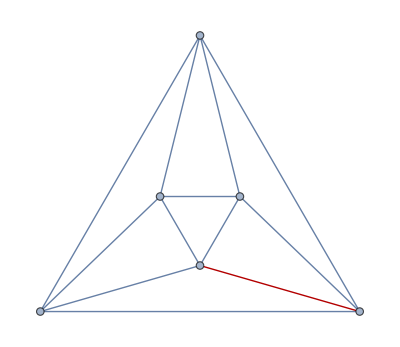
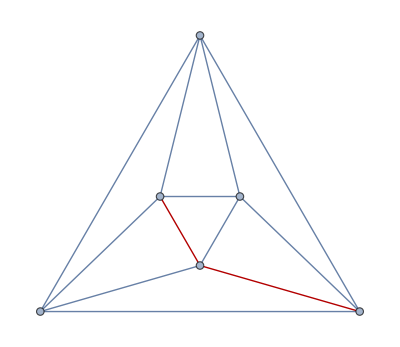
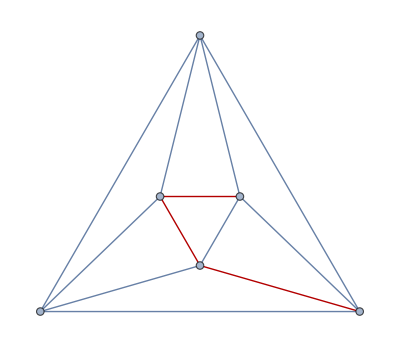
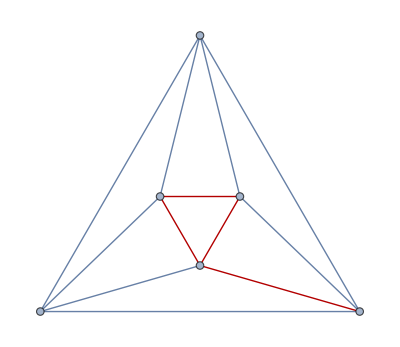
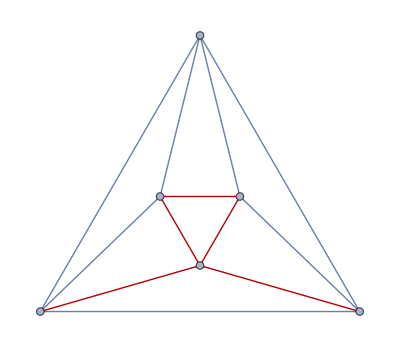
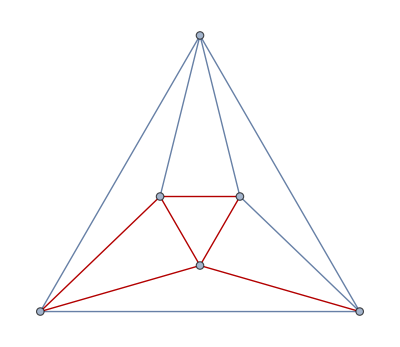
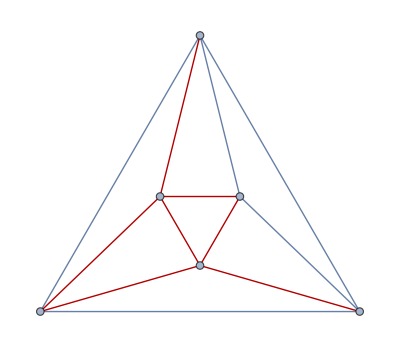
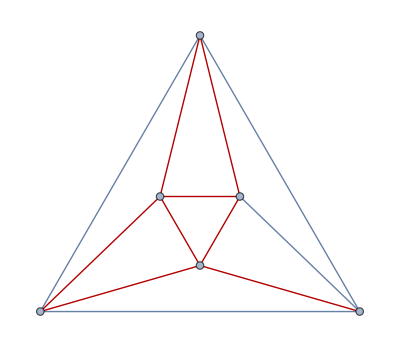

```mathematica
g=GraphData["OctahedralGraph"];
ec=FindEulerianCycle[g];
Table[HighlightGraph[g,Part[First[%],1;;i]],{i,Length[First[ec]]}]
```

```mathematica
Sum[StirlingS2[5,k],{k,1,5}]
```

52

```mathematica
BellB[5]
```

52

```mathematica
Map[{#,PrimeNu[#]}&,{210,60,36,24,16}]//tf
```

210 | 4
60 | 3
36 | 2
24 | 2
16 | 1